```mathematica
(DictionaryLookup[RegularExpression[".{"<>ToString[#]<>"}"]]//Length)&/@Range[25]
```

{2,118,923,3484,6789,10549,13989,14583,13160,10624,7532,4949,2935,1508,784,324,167,60,21,10,3,3,1,0,0}

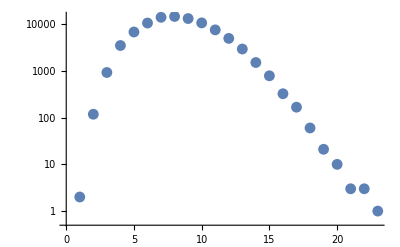

```mathematica
ListLogPlot@%113
```

```mathematica
Clear[numdigs,numlets,numwords,succwords];
numdigs[num_,n_]:=numdigs[num,n]=RealDigits[N[num,n],26][[1]];
numlets[num_,n_]:=numlets[num,n]=FromCharacterCode[97+#]&/@numdigs[num,n];
numwords[num_,n_,l_]:=numwords[num,n,l]=StringJoin/@Partition[numlets[num,n],l,1];
succwords[num_,n_,l_]:=succwords[num,n,l]=Flatten[DictionaryLookup/@numwords[num,n,l]];
```

```mathematica
succwords[Pi,100000,#]&/@Range[6]
```

```mathematica
First/@%234
```

{a,rs,rod,trod,steel,oxygen}

```mathematica
StringJoin@numlets[E,3300]
```

csronomlbjzwcuwzwhgrtwgjxkezsrlnytlnvrypoxjgtmltffdpeenwkngcrprlljmrmfmertntkqfpgfpthrlwipnzzkahbjbhngkyonjhimvtgfvepoqlytqmchdkgwqmevjmzfzcjqouqhtnttletmtnsziakvtkbkhykgjszmjmsyeivmnohooczfemkntyxkjaodvymfsixodsutdmucgzeoltowranzlwizodbaxglgfreuolxxrimpeukhytfgztrgxaqbmfsrxujmlfnshxkcvxrqbigwfkhjrtmbrffdydjvpfyvxnjrytqrldveekqarkrpordvajmvlllveglngqpfcwejveakkvetznwmztqpewvqpeioheuvvlihbpamqhbtrifltgvcmporstadjxwoakmdjxeadptozbhnjhwvcrrfrmbbcxaunuxvtiuuxnutrfkbgxxcagmrxilkfrlsofrrdqwncawvydexvdwsdxipoenggppbjqcewdkslmnnqyklwkqzdmqzpxztleqroecuskhnkakgbzsdgmujoataacogibmcoznnjggnswtzmpaandinfznjqzlzcmzlxphhxoucqodhokbgxijnpoonzoflgsceyrgruqcdcpxddpzxmlblbowghzrmihtplmfetibsgtdjidjlakfhufoufximvpfdafgctfiggmwmigcauasjjovzbhpwolpzawswynvcuupghlficbliuljujvzwwcbsubxgwglgzegluycjuxavosjrstfrkcmgzggwnzcbpqihbqehjavpqrvtxdzdnmaqdagbclvrvskrmaevhojsnabtptozvkaxwonqqtkaddhoxosopyaicjesvvuvmxufsjizbppvoyfqrvixtvgsjyhlquqzlwiniqcwlfiyhreknsjvsimoqggiwhltyezztjqggsnwqvcdweblldavftuncdrjtppuimqtybzesfvolvqzpczejxqunptvnqakjodlkwoaiaqwgyrvvvqhxmcxfvizzqjtuoekqchbrtdjhaalcinkctcqfwqgjmphiqnnifnnpnagglyzrtsxyprfohfvzjcfyzxiwhdvryucrziqpweisphjprngtqbuizcxvrahfdeygohkpydteytalrwgfytrvwpsymaadyrlslszgxwazlwkluycdmlxncrmwemwptenigurvziybmppzncrkwsktlmmpjtknxwtphxuplbhujrmssjxfjplhiewxtrxnedqcizpmpkfyqjysuwozwoqrvpaajedipdxhclkqwoqglgerlwveszimsfvrbnmpdbklzycbklvpprbjqsncepyhbpfcggpsqknbtopvrksjxboqteunxkbyqgwfsgewrjddxxsbspwomacculmpiosmrxpowbwoemzmkrceirmahitqfyokyehiypzscsfryrbnzveuaajzweviifqbotozxomhliuegguduigbwnjkyscpscnoeqnunwderzwxsqzjmegeclqdgnvdguchdrvxlzsxbepwonuozrexrmjzvqepcriigcljkvwfqusggidzfqjiyrdqxwmyzpcvivmufohjyylobaqhkldhnwozxvlzeccvgvocrcqdrttjmlrngpzpbldoqwpdjjifyofznxwrnqktagfturznurettkplubfxuffxlzbamvjwrstkhhfjcnfcpaxlmagjshyichymwqjbfixfugiljcvkxauyemswuhwpfanycumrntnxusxjcslzwupgnbeacmxxvqaqlrxwlxvgvbgdqmmxgvatxrlthbncdrexyrtflrrtdoulgmrwivwlbglkuvxdbdefbtatvwaghnuezjgvojbqldbhaympyebrgpcjgbmndnruoipsiiqoprwspzptqakisdvlvaddoaharogjkyoemxpnkbdophmthumeklqubupeztctqrvehsgezarbqmdvevzfmsyyesfrcbagglrwzrtxmsbzdbcsipaglcgexlfkbdujrrgejzlaocitmikfmcfblheexidkswgdvksiahvriehtqqxrafdqvwfgtpzqahsfjemvuxlwyvmgzrtgwtqebqsbiqvgudonhscbroitzszztjsberbgivqplllhpqvrjwqbbmcohulzrmayifjnoncnkpygzaavspibgfdaxykjycuihyinchdldhmstgmdyawqfwangelbixevtigtalyqrvtfomstvqyxnwbiyxdlgpisjenpfvqwzvwudwvpvmedc

```mathematica
succwords[E,1000000,7]
```

{}

```mathematica
succwords[Pi,1000000,7]
```

{subplot,conjure}